```mathematica
<<CSL`OdeUtils`;
RungeKuttaCatalog[]
x=RungeKuttaCatalog["rk4"];
p=4;
```

Dataset[<>]

```mathematica
RungeKuttaQ[x]
RungeKuttaPairQ[x]
RungeKuttaTableau[x]
RungeKuttaFsalQ[x]
RungeKuttaA[x,p+1]//N
RungeKuttaB[x,p+1]//N
RungeKuttaC[x,p+1]//N
RungeKuttaD[x]//N
RungeKuttaE[x,p+1]//N
```

True

False

0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0 | 0
1 | 0 | 0 | 1 | 0
 | 1/6 | 1/3 | 1/3 | 1/6

False

0.0145046

RungeKuttaB[<|A→{{0.,0.,0.,0.},{0.5,0.,0.,0.},{0.,0.5,0.,0.},{0.,0.,1.,0.}},b→{0.166667,0.333333,0.333333,0.166667},c→{0.,0.5,0.5,1.}|>,5.]

RungeKuttaC[<|A→{{0.,0.,0.,0.},{0.5,0.,0.,0.},{0.,0.5,0.,0.},{0.,0.,1.,0.}},b→{0.166667,0.333333,0.333333,0.166667},c→{0.,0.5,0.5,1.}|>,5.]

1.

RungeKuttaE[<|A→{{0.,0.,0.,0.},{0.5,0.,0.,0.},{0.,0.5,0.,0.},{0.,0.,1.,0.}},b→{0.166667,0.333333,0.333333,0.166667},c→{0.,0.5,0.5,1.}|>,5.]

1+z+z^2/2+z^3/6+z^4/24

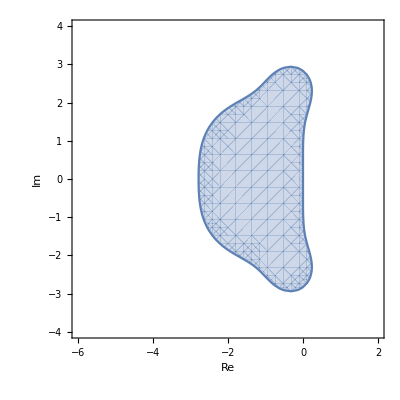

1+z+z^2/2+z^3/6+z^4/24

1

-1/576 y^6 (-8+y^2)

False

False

```mathematica
RungeKuttaLinearStability[x,z]//Simplify
RungeKuttaLinearStabilityPlot[x]
RungeKuttaLinearStabilityP[x,z]//Simplify
RungeKuttaLinearStabilityQ[x,z]//Simplify
RungeKuttaLinearStabilityE[x,y]//Simplify
RungeKuttaAStableQ[x]
RungeKuttaStifflyAccurateQ[x]
```